```mathematica
(* Exploring outside prisoner's dilemma *)
```

```mathematica
Clear["Global`*"]
```

```mathematica
(* 4-state *)
(*Reward structure for player a (initial, CC, CD, DC, DD)*)
Rmat ={R,S,T,P};
(*Transition matrix (P_ij = prob. of going from i to j)*)
Pmat = {{a1*b1,a1*(1-b1),(1-a1)*b1,(1-a1)*(1-b1)},{a2*b2,a2*(1-b2),(1-a2)*b2,(1-a2)*(1-b2)},{a3*b3,a3*(1-b3),(1-a3)*b3,(1-a3)*(1-b3)},{a4*b4,a4*(1-b4),(1-a4)*b4,(1-a4)*(1-b4)}};
(*Initial condition*)
p0 = {a0*b0,a0*(1-b0),(1-a0)*b0,(1-a0)*(1-b0)};
(*Direction solution of the Bellman equation*)
V=p0.Inverse[IdentityMatrix[4] - gamma*Pmat].Rmat;
FullSimplify[Series[V,{gamma,0,2}]]
```

$Aborted

```mathematica
a=Inverse[IdentityMatrix[4] - gamma*Pmat].Rmat;
FullSimplify[Series[Total[a],{gamma,0,1}]]
```

(P+R+S+T)+((4-a4+a1 (-1+b1)-b1+a2 (-1+b2)-b2+a3 (-1+b3)-b3+(-1+a4) b4) P+a2 b2 R+a3 b3 R+a4 b4 R+a2 S+a3 S+a4 S-a2 b2 S-a3 b3 S-a4 b4 S+a1 (S+b1 (R-S-T))+b1 T+(b2-a2 b2+b3-a3 b3+b4-a4 b4) T) gamma+O[gamma]^2

```mathematica
(*5-state -----------------------------------------------------*)
(*Reward structure for player a (initial, CC, CD, DC, DD)*)
Rmat ={0,R,S,T,P};
(*Transition matrix (P_ij = prob. of going from i to j)*)
Pmat = {{0,a0*b0,a0*(1-b0),(1-a0)*b0,(1-a0)*(1-b0)},{0,a1*b1,a1*(1-b1),(1-a1)*b1,(1-a1)*(1-b1)},{0,a2*b2,a2*(1-b2),(1-a2)*b2,(1-a2)*(1-b2)},{0,a3*b3,a3*(1-b3),(1-a3)*b3,(1-a3)*(1-b3)},{0,a4*b4,a4*(1-b4),(1-a4)*b4,(1-a4)*(1-b4)}};
(*Direction solution of the Bellman equation*)
V=Inverse[IdentityMatrix[5] - gamma*Pmat].Rmat;
FullSimplify[Series[V[[1]],{gamma,0,2}]]
```

((-1+a0) (-1+b0) P+a0 (S+b0 (R-S-T))+b0 T) gamma+(-(-1+a3 b0+b0 b3-a3 b0 b3+a4 (-1+b0) (-1+b4)+b4-b0 b4+a0 (a2 (-1+b0) (-1+b2)+b2-b4+b0 (a1+b1-a1 b1-b2+a3 (-1+b3)-b3+b4)+a4 (-1+b0+b4-b0 b4))) P+a3 b0 b3 R+a4 b4 R-a4 b0 b4 R+a4 S+a3 b0 S-a4 b0 S-a3 b0 b3 S-a4 b4 S+a4 b0 b4 S+b0 b3 T-a3 b0 b3 T+b4 T-a4 b4 T-b0 b4 T+a4 b0 b4 T+a0 (-a3 b0 b3 R-a4 b4 R+a4 b0 b4 R-a4 S-a3 b0 S+a4 b0 S+a3 b0 b3 S+a4 b4 S-a4 b0 b4 S+a1 b0 (S+b1 (R-S-T))+(b2+(-1+a4) b4+b0 (b1-b2+(-1+a3) b3+b4-a4 b4)) T+a2 (-1+b0) (-S+b2 (-R+S+T)))) gamma^2+O[gamma]^3

```mathematica
(*Series expansion of the solution*)
Series[V,{gamma,0,1}]
```

{(P-a0 P-b0 P+a0 b0 P+a0 b0 R+a0 S-a0 b0 S+b0 T-a0 b0 T) gamma+O[gamma]^2,R+(P-a1 P-b1 P+a1 b1 P+a1 b1 R+a1 S-a1 b1 S+b1 T-a1 b1 T) gamma+O[gamma]^2,S+(P-a2 P-b2 P+a2 b2 P+a2 b2 R+a2 S-a2 b2 S+b2 T-a2 b2 T) gamma+O[gamma]^2,T+(P-a3 P-b3 P+a3 b3 P+a3 b3 R+a3 S-a3 b3 S+b3 T-a3 b3 T) gamma+O[gamma]^2,P+(P-a4 P-b4 P+a4 b4 P+a4 b4 R+a4 S-a4 b4 S+b4 T-a4 b4 T) gamma+O[gamma]^2}

```mathematica
(*Reward structure for player b (initial, CC, CD, DC, DD)*)
(*Note: CD still means player a = C, player b = D*)
Rmat2 ={0,R,T,S,P};
(*Direction solution of the Bellman equation*)
V2=Inverse[IdentityMatrix[5] - gamma2*Pmat].Rmat2;
```

```mathematica
Series[V2,{gamma2,0,1}]
```

{(P-a0 P-b0 P+a0 b0 P+a0 b0 R+b0 S-a0 b0 S+a0 T-a0 b0 T) gamma2+O[gamma2]^2,R+(P-a1 P-b1 P+a1 b1 P+a1 b1 R+b1 S-a1 b1 S+a1 T-a1 b1 T) gamma2+O[gamma2]^2,T+(P-a2 P-b2 P+a2 b2 P+a2 b2 R+b2 S-a2 b2 S+a2 T-a2 b2 T) gamma2+O[gamma2]^2,S+(P-a3 P-b3 P+a3 b3 P+a3 b3 R+b3 S-a3 b3 S+a3 T-a3 b3 T) gamma2+O[gamma2]^2,P+(P-a4 P-b4 P+a4 b4 P+a4 b4 R+b4 S-a4 b4 S+a4 T-a4 b4 T) gamma2+O[gamma2]^2}

```mathematica
(*Game type ------------------------------------------------------*)
(*Prisoner's dilemma*)
R=3;S=0;T=5;P=1;
(*Battle of the sexes*)
R=0;S=1;T=2;P=0;

(*Actual*)
R=0;S=-1;T=0;P=0;

R=3;S=0;T=5;P=1;
```

```mathematica
(*Generic crit. gamma -------------------------------------------------------------------------------------------------------------------------------*)
```

{gamma→0.666667}

{gamma→0.666667}

{gamma→0.666667}

«2 more identical outputs»

{gamma2→0.833333}

{gamma2→0.833333}

{gamma2→0.636573}

{gamma2→0.833333}

{gamma2→0.769231}

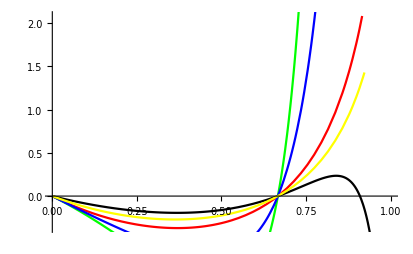

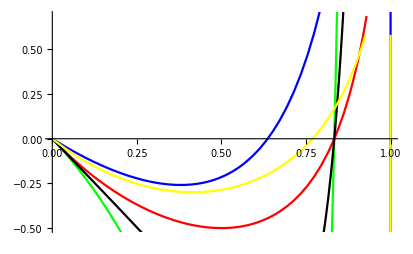

```mathematica
Clear[a0,a1,a2,a3,a4,b0,b1,b2,b3,b4,gamma,gamma2];

(*Init param ------------------------------------------------------*)
(*All-coop*)
a0v = 1;a1v=1;a2v=1;a3v=1;a4v=1;
b0v=1; b1v=1;b2v=1;b3v=1;b4v=1;
(*All-defect*)
a0v = 0;a1v=0;a2v=0;a3v=0;a4v=0;
b0v=0; b1v=0;b2v=0;b3v=0;b4v=0;
(*All-Random*)
a0v = 0.5;a1v=0.5;a2v=0.5;a3v=0.5;a4v=0.5;
b0v=0.5; b1v=0.5;b2v=0.5;b3v=0.5;b4v=0.5;
(*tit-for-tat*)
a0v = 1;a1v=1;a2v=0;a3v=1;a4v=0;
b0v=1; b1v=1;b2v=1;b3v=0;b4v=0;
(*Everything positive regime*)
a0v = 1;a1v=1;a2v=0.2;a3v=1;a4v=0.5;
b0v=1; b1v=1;b2v=1;b3v=0;b4v=0.5;

(*Actual*)
a0v = 1;a1v=1;a2v=0.2;a3v=1;a4v=0.5;
b0v=1; b1v=1;b2v=1;b3v=0;b4v=0.5;


(*------------------------------------------------------*)

(* V1 *)
a0=a0v;a1=a1v;a2=a2v;a3=a3v;a4=a4v;
b0=b0v;b1=b1v;b2=b2v;b3=b3v;b4=b4v;

Clear[a0];
Va0 = D[Total[V],a0];
a0=a0v;
FindRoot[Va0,{gamma,0.8}]
plt0 = Plot[Va0,{gamma,0,1},PlotStyle->Red];

Clear[a1];
Va1 = D[Total[V],a1];
a1=a1v;
FindRoot[Va1,{gamma,0.8}]
plt1 = Plot[Va1,{gamma,0,1},PlotStyle->Green];

Clear[a2];
Va2 = D[Total[V],a2];
a2=a2v;
FindRoot[Va2,{gamma,0.8}]
plt2 = Plot[Va2,{gamma,0,1},PlotStyle->Blue];

Clear[a3];
Va3 = D[Total[V],a3];
a3=a3v;
FindRoot[Va3,{gamma,0.8}]
plt3 = Plot[Va3,{gamma,0,1},PlotStyle->Black];

Clear[a4];
Va4 = D[Total[V],a4];
a4=a4v;
FindRoot[Va4,{gamma,0.8}]
plt4 = Plot[Va4,{gamma,0,1},PlotStyle->Yellow];

pltVsum = Plot[Va0+Va1+Va2+Va3+Va4,{gamma,0,1},PlotStyle->Brown];

(* V2 *)
a0=a0v;a1=a1v;a2=a2v;a3=a3v;a4=a4v;
b0=b0v;b1=b1v;b2=b2v;b3=b3v;b4=b4v;

Clear[b0];
Vb0 = D[Total[V2],b0];
b0=b0v;
FindRoot[Vb0,{gamma2,0.8}]
pltb0 = Plot[Vb0,{gamma2,0,1},PlotStyle->Red];

Clear[b1];
Vb1 = D[Total[V2],b1];
b1=b1v;
FindRoot[Vb1,{gamma2,0.8}]
pltb1 = Plot[Vb1,{gamma2,0,1},PlotStyle->Green];

Clear[b2];
Vb2 = D[Total[V2],b2];
b2=b2v;
FindRoot[Vb2,{gamma2,0.8}]
pltb2 = Plot[Vb2,{gamma2,0,1},PlotStyle->Blue];

Clear[b3];
Vb3 = D[Total[V2],b3];
b3=b3v;
FindRoot[Vb3,{gamma2,0.95}]
pltb3 = Plot[Vb3,{gamma2,0,1},PlotStyle->Black];

Clear[b4];
Vb4 = D[Total[V2],b4];
b4=b4v;
FindRoot[Vb4,{gamma2,0.8}]
pltb4 = Plot[Vb4,{gamma2,0,1},PlotStyle->Yellow];

pltV2sum = Plot[Vb0+Vb1+Vb2+Vb3+Vb4,{gamma2,0,1},PlotStyle->Brown];

Show[plt0,plt1,plt2,plt3,plt4]
Show[pltb0,pltb1,pltb2,pltb3,pltb4]
```